```mathematica
(* Assuming ω is real so conjugates go away *)
```

```mathematica
$Assumptions={Element[{ω},Reals]};
(* Setting T and B to unity, since they don't matter for this analysis *)
T = 1;
B = 1;
plus = 1/Sqrt[2] * {{1,1}};
(* Just some pulse definitions *)
nhat = {0, 1, 0};
σ = {PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
P4 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P8 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/8;
mP4 = MatrixExp[ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P2 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/2;
```

```mathematica
(* Defining the free evolution unitary *)
Theta[t2_,t1_]:= Sin[ω*t2]/ω - Sin[ω*t1]/ω;
U[t2_, t1_] := MatrixExp[-ⅈ*B*PauliMatrix[3]*Theta[t2, t1]];
Dagger[X_] := Refine[Conjugate[Transpose[X]], {θ ∈ Reals, ω ∈ Reals}];
```

```mathematica
(* We'll assume everything is equally spaced, this is technically wlog since you can alwayas consider a longer sequence...*)
(* Produces the associated Z string unitary on the jth pulse*)
Zj[Ps_, j_] :=   Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[i=1,i<a + 1,i++,rtn=U[T/a*(i), T/a*(i-1)].list[[i]].rtn;
If[ i == j, rtn = PauliMatrix[3].rtn]];
rtn];
(* See the overleaf document. Strings with two Z's in them. *)
Vij[Ps_, i_, j_] := plus.Dagger[Zj[Ps, i]].Zj[Ps, j].Transpose[plus]//FullSimplify;
```

```mathematica
(* In general, it is frequency dependent*)
Ps = {P, P};
```

```mathematica
Vij[Ps, 1, 2]
```

{{1/(√2),1/(√2)}}.Conjugate[Transpose[{{ⅇ^((ⅈ (Sin[ω/2]-Sin[ω]))/ω),0},{0,ⅇ^((ⅈ (-Sin[ω/2]+Sin[ω]))/ω)}}.P.{{ⅇ^(-(ⅈ Sin[ω/2])/ω),0},{0,-ⅇ^((ⅈ Sin[ω/2])/ω)}}.P.{{1,0},{0,1}}]].{{ⅇ^((ⅈ (Sin[ω/2]-Sin[ω]))/ω),0},{0,-ⅇ^((ⅈ (-Sin[ω/2]+Sin[ω]))/ω)}}.P.{{ⅇ^(-(ⅈ Sin[ω/2])/ω),0},{0,ⅇ^((ⅈ Sin[ω/2])/ω)}}.P.{{1/(√2)},{1/(√2)}}

```mathematica
(* A Z expectation after j pulses, see the overleaf *)
Vj[Ps_, j_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[i=1,i<a + 1,i++,If[ i < j + 1, rtn=U[T/a*(i), T/a*(i-1)].list[[i]].rtn]];
plus.Dagger[rtn].PauliMatrix[3].rtn.Transpose[plus]]
```

```mathematica
(* In general, it is frequency dependent *)
Ps = {P4, P4, P4};
Vj[Ps, 1]//FullSimplify
Vj[Ps, 2]//FullSimplify
Vj[Ps, 3]//FullSimplify
```

{{-1/(√2)}}

{{-Cos[Sin[ω/3]/ω]^2}}

{{1/8 (-2 √2-2 √2 Cos[(2 Sin[ω/3])/ω]-(-2+√2) Cos[(8 Sin[ω/6]^2 Sin[ω/3])/ω]+2 √2 Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]-(2+√2) Cos[(2 Sin[(2 ω)/3])/ω])}}

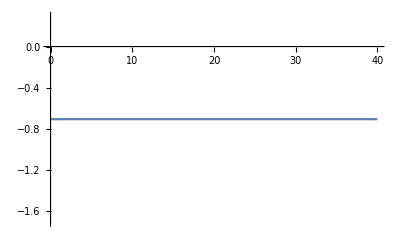

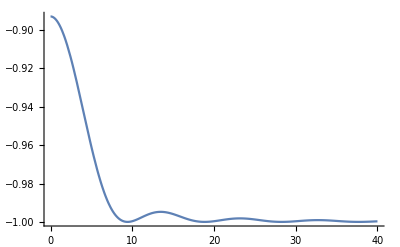

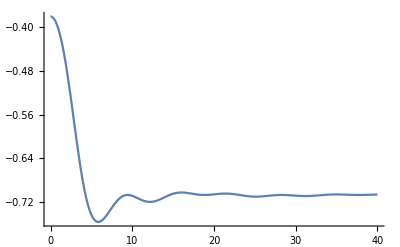

```mathematica
(*Plotting the behavior*)
Plot[-1/(√2),{ω, 0, 40},PlotRange->Full]
Plot[{{-Cos[Sin[ω/3]/ω]^2}}, {ω, 0, 40}, PlotRange->Full]
Plot[1/8 (-2 √2-2 √2 Cos[(2 Sin[ω/3])/ω]-(-2+√2) Cos[(8 Sin[ω/6]^2 Sin[ω/3])/ω]+2 √2 Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]-(2+√2) Cos[(2 Sin[(2 ω)/3])/ω]), {ω, 0 ,40},PlotRange->Full]
```

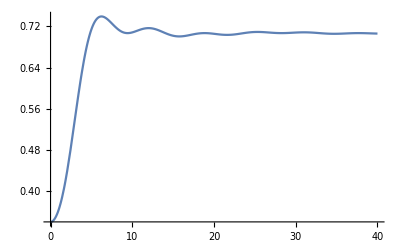

```mathematica
(*Plotting the product of the last two, since this is what shows up, see the overleaf*)
Plot[{{-Cos[Sin[ω/3]/ω]^2}} * 1/8 (-2 √2-2 √2 Cos[(2 Sin[ω/3])/ω]-(-2+√2) Cos[(8 Sin[ω/6]^2 Sin[ω/3])/ω]+2 √2 Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]-(2+√2) Cos[(2 Sin[(2 ω)/3])/ω]), {ω, 0 ,40}, PlotRange->Full]
```

```mathematica
(* See the overleaf, Vij + Vij^{\dagger} shows up - it is also in general frequency dependent. But note, positive in this case. *)
Ps = {P4, mP4, mP4};
(Vij[Ps, 1,3] + Conjugate[Vij[Ps, 1,3]])//FullSimplify
```

{{1-Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]}}

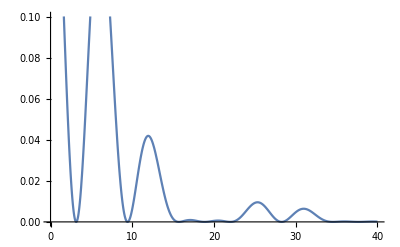

```mathematica
Plot[{{1-Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]}}, {ω, 0, 40}]
```

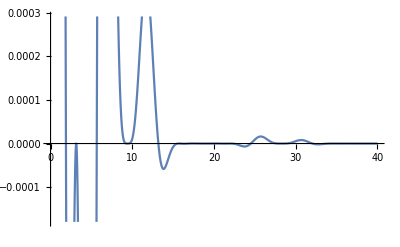

```mathematica
Plot[(1-Cos[(2 (Sin[ω/3]-Sin[(2 ω)/3]))/ω]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2], {ω, 0, 40}]
```

```mathematica
Ps = {P4, mP4, mP4};
integrand = (Vij[Ps, 1,3] + Conjugate[Vij[Ps, 1,3]]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2] - 2*Vj[Ps, 1] * Vj[Ps, 3]* Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2];
bound = 1000;
NIntegrate[integrand, {ω, 0, bound}]
```

{{-0.0382442-1.20885×10^-18 ⅈ}}

```mathematica
Ps = {P4, P4, mP4};
integrand = (Vij[Ps, 1,3] + Conjugate[Vij[Ps, 1,3]]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2] - 2*Vj[Ps, 1] * Vj[Ps, 3]* Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2];
bound = 1000;
NIntegrate[integrand, {ω, 0, bound}]
```

{{-0.0572615-7.80451×10^-19 ⅈ}}

```mathematica
Ps = {P4, P4, P4};
integrand = (Vij[Ps, 1,3] + Conjugate[Vij[Ps, 1,3]]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2] - 2*Vj[Ps, 1] * Vj[Ps, 3]* Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2];
bound = 10000000000;
NIntegrate[integrand, {ω, 0, bound}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {19.0437}. NIntegrate obtained 0.0681382-2.59383×10^-18 ⅈ and 0.0588914 for the integral and error estimates.

{{0.0681382}}

```mathematica
(* Other j value for same i*)
Ps = {P4, P4, P4};
integrand = (Vij[Ps, 1,2] + Conjugate[Vij[Ps, 1,2]]) * Theta[T/3 *1, 0]*Theta[T/3 *2, T/3 *1] - 2*Vj[Ps, 1] * Vj[Ps, 2]* Theta[T/3 *1, 0]*Theta[T/3 *2, T/3 *1];
bound = 10000000;
NIntegrate[integrand, {ω, 0, bound}]
```

NIntegrate::levmaxord: -(2 ((ⅇ^(ⅈ Power[«2»] Sin[«1»]) «1» (-Power[«2»] «1» Cos[«1»]-«1»)«1»«1»)/(√2)+(ⅇ^(ⅈ «1» «1») «1» («1»-«1»)-«1»)/(√2)) ((«1»)/(√2)+(«1»+«1»)/(√2)) Sin[ω/3] (-Sin[ω/3]/ω+Sin[(2 ω)/3]/ω))/ω is a Levin function of differential order 2048 which exceeds value of option "MaxOrder" -> 50. Treating -(2 ((ⅇ^(ⅈ Power[«2»] Sin[«1»]) «1» (-Power[«2»] «1» Cos[«1»]-«1»)«1»«1»)/(√2)+(ⅇ^(ⅈ «1» «1») «1» («1»-«1»)-«1»)/(√2)) ((«1»)/(√2)+(«1»+«1»)/(√2)) Sin[ω/3] (-Sin[ω/3]/ω+Sin[(2 ω)/3]/ω))/ω as a non-Levin function.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.207884}. NIntegrate obtained 0.0259877+3.37159×10^-15 ⅈ and 0.10038 for the integral and error estimates.

{{0.0259877}}

```mathematica
Ps = {P4, P4, P4};
integrand = (Vi[Ps, 1]^21,3]]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2] - 2*Vj[Ps, 1] * Vj[Ps, 3]* Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2];
bound = 1000;
NIntegrate[integrand, {ω, 0, bound}]

Ps = {PauliMatrix[4], PauliMatrix[4], PauliMatrix[4]};
integrand = (Vij[Ps, 1,3] + Conjugate[Vij[Ps, 1,3]]) * Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2] - 2*Vj[Ps, 1] * Vj[Ps, 3]* Theta[T/3 *1, 0]*Theta[T/3 *3, T/3 *2];
bound = 1000;
NIntegrate[integrand, {ω, 0, bound}]
```

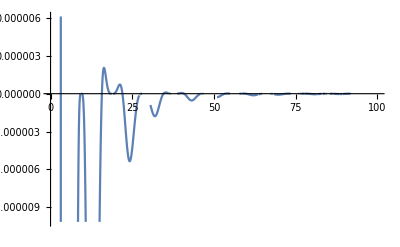

```mathematica
Plot[(Vij[Ps, 1,2] + Conjugate[Vij[Ps, 1,2]]) * Theta[T/3 *1, 0]*Theta[T/3 *2, T/3 *1] - 2*Vj[Ps, 1] * Vj[Ps, 2]* Theta[T/3 *1, 0]*Theta[T/3 *2, T/3 *1], {ω, 0, 100}]
```

```mathematica
Vj[Ps, 1] * Vj[Ps, 2]* Theta[T/3 *1, 0]*Theta[T/3 *2, T/3 *1]/.ω->∞
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√2 Cos[π/8] Sin[π/8]+(Cos[π/8]^2-Sin[π/8]^2)/(√2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{Interval[{0,0}]}}

```mathematica
Vij[Ps, 1, 2]
```

{{1/(√2)-1/2 ⅈ Sin[(2 Sin[ω/3])/ω]}}

```mathematica
Vj[{P4}, 1]//FullSimplify
```

{{-1/(√2)}}

```mathematica
(* Let's randomly verify for different choices of pulses. *)
NullGen[i_]:=Null
CondEval[j_, vjs_, Ps_] := If[vjs[[j]]==Null, Vj[Ps, j], vjs[[j]]]
BoundEval[Ps_] :=   Module[{list= Ps,a},a=Length[list];
rt = 0; (* Using the word rtn was breaking it... *)
vjs = Array[NullGen, a];
For[j=1,j<a + 1,j++,
vjs[[j]] = CondEval[j,vjs, list][[1]][[1]]//FullSimplify;
jonepoint = vjs[[j]];
For[l=1,l<j ,l++,
vjs[[l]]=CondEval[l,vjs, list][[1]][[1]]//FullSimplify;
twopoint = Vij[list, l,j][[1]][[1]];
twoonepoint = 2*vjs[[l]]*vjs[[j]] ;
twotheta = Theta[T/a *l,(T/a)*(l-1)]*Theta[T/a *j, T/a*(j-1)];
rt +=twotheta * (twopoint + Conjugate[twopoint]) - twoonepoint * twotheta];
rt -= Theta[T/a *j, T/a *(j-1)]^2*vjs[[j]]^2];
rt]
```

```mathematica
NIntegrate[BoundEval[{P4, PauliMatrix[1], P4, PauliMatrix[2]}], {ω, 0 ,10000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {702.97}. NIntegrate obtained -1.32951+3.39901×10^-18 ⅈ and 0.0013295 for the integral and error estimates.

-1.32951+3.39901×10^-18 ⅈ

```mathematica
Integrate[BoundEval[{P4}]//FullSimplify, {ω, 0, ∞}]
```

-π/4

```mathematica
Integrate[BoundEval[{PauliMatrix[4]}]//FullSimplify, {ω, 0, ∞}]
```

0

```mathematica
NIntegrate[BoundEval[{PauliMatrix[4], P4}]//FullSimplify, {ω, 0, 1000000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {33.2834}. NIntegrate obtained -0.275374 and 0.0480419 for the integral and error estimates.

-0.275374

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1953.13}. NIntegrate obtained -1.12369 and 0.938268 for the integral and error estimates.

-1.12369

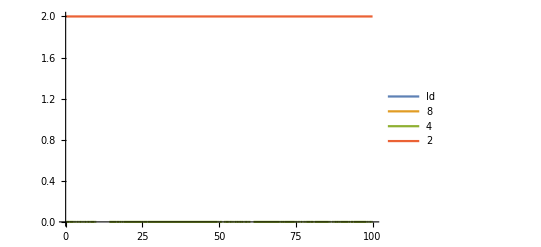

Part::partd: Part specification PauliMatrix⟦4⟧ is longer than depth of object.

2 Re[{{ⅇ^(-(ⅈ Sin[ω/2])/ω)/(√2),ⅇ^((ⅈ Sin[ω/2])/ω)/(√2)}}.PauliMatrix⟦4⟧.{{0,ⅇ^((ⅈ Sin[ω/2])/ω)},{ⅇ^(-(ⅈ Sin[ω/2])/ω),0}}.PauliMatrix⟦4⟧.{{1/(√2)},{1/(√2)}}]

```mathematica
Xij[Ps_, i_, j_] :=   Module[{list= Ps,a},a=Length[list];
rtn1 = PauliMatrix[4];
For[l=1,l<i + 1,l++,rtn1=U[T/a*(l), T/a*(l-1)].list[[l]].rtn1;];
rtn1 = Dagger[rtn1].PauliMatrix[3].rtn1;
rtn2 = PauliMatrix[4];
For[l=1,l<j + 1,l++,rtn2=U[T/a*(l), T/a*(l-1)].list[[l]].rtn2;];
rtn2 = Dagger[rtn2].PauliMatrix[3].rtn2;
x = plus.rtn1.PauliMatrix[1].rtn2.Transpose[plus];
x + Conjugate[x]]
Plot[{Xij[{PauliMatrix[4],PauliMatrix[4]}, 1, 2]//FullSimplify,Xij[{P8,PauliMatrix[4]}, 1, 2]//FullSimplify, Xij[{P4,PauliMatrix[4]}, 1, 2]//FullSimplify, Xij[{P2,PauliMatrix[4]}, 1, 2]//FullSimplify}, {ω, 0, 100},  PlotLegends->{"Id", "8",  "4","2"}, PlotRange->{0,2}]
```

```mathematica
f=Xij[{P8,PauliMatrix[4]}, 1, 1][[1]][[1]]//FullSimplify
```

1/2 (2+√(2+√2)-(-2+√(2+√2)) Cos[(2 Sin[ω/2])/ω])

```mathematica
FindMinimum[f,{ω,40}]
```

{1.99991,{ω→40.7426}}

```mathematica
vals=Reap[soln=y[ω]/.First[NDSolve[{y'[ω]==Evaluate[D[f,ω]],y[40]==(f/.ω->40)},y[ω],{ω,40,60},Method->{"EventLocator","Event"->y'[ω],"EventAction":>Sow[{ω,y[ω]}]}]]][[2,1]];
```

Unset::wrsym: Symbol Dot is Protected.

Set::write: Tag Dot in ({{1/(√2),1/(√2)}}.1/(√2))[40.7426] is Protected.

Unset::wrsym: Symbol Dot is Protected.

Set::write: Tag Dot in ({{1/(√2),1/(√2)}}.1/(√2))[43.9823] is Protected.

Unset::wrsym: Symbol Dot is Protected.

General::stop: Further output of Unset::wrsym will be suppressed during this calculation.

Set::write: Tag Dot in ({{1/(√2),1/(√2)}}.1/(√2))[47.0389] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
vals
```

{{40.7426,({{1/(√2),1/(√2)}}.1/(√2))[40.7426]},{43.9823,({{1/(√2),1/(√2)}}.1/(√2))[43.9823]},{47.0389,({{1/(√2),1/(√2)}}.1/(√2))[47.0389]},{50.2655,({{1/(√2),1/(√2)}}.1/(√2))[50.2655]},{53.3321,({{1/(√2),1/(√2)}}.1/(√2))[53.3321]},{56.5487,({{1/(√2),1/(√2)}}.1/(√2))[56.5487]},{59.6232,({{1/(√2),1/(√2)}}.1/(√2))[59.6232]}}

```mathematica
Length[vals]
```

7

```mathematica
newvals = {};
```

```mathematica
For[i=1,i < Length[vals], i++, 
newvals = Append[newvals, {vals[[i]][[1]],0}];
newvals;
Print[newvals]]
```

{{40.7426,0}}

{{40.7426,0},{43.9823,0}}

{{40.7426,0},{43.9823,0},{47.0389,0}}

{{40.7426,0},{43.9823,0},{47.0389,0},{50.2655,0}}

{{40.7426,0},{43.9823,0},{47.0389,0},{50.2655,0},{53.3321,0}}

{{40.7426,0},{43.9823,0},{47.0389,0},{50.2655,0},{53.3321,0},{56.5487,0}}

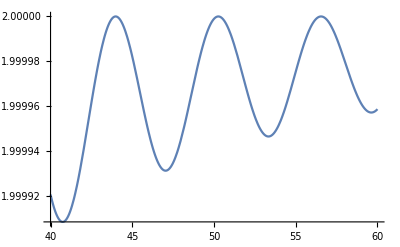

```mathematica
Plot[f,{ω,40,60},Epilog->{PointSize[Medium],Red,Point[newvals]}]
```

```mathematica
{{a,b}}=InterpolatingFunctionDomain[Head[f[ω]]];
criticalPoints=ω/.RootSearch[f'[ω]==0,{ω,a,b}];
mins=Select[criticalPoints,f''[#]>0&];
maxs=Select[criticalPoints,f''[#]<0&];
```

Set::shape: Lists {{a,b}} and InterpolatingFunctionDomain[1/2 (2+√(2+√2)-(-2+√(2+Power[«2»])) Cos[(2 Sin[Times[«2»]])/ω])] are not the same shape.

ReplaceAll::reps: {RootSearch[(1/2 (2+√Plus[«2»]-Plus[«2»] Cos[«1»]))'[ω]==0,{ω,a,b}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["Ersek`RootSearch`"]
```

Get::noopen: Cannot open Ersek`RootSearch`.

Needs::nocont: Context Ersek`RootSearch` was not created when Needs was evaluated.

$Failed

1

100

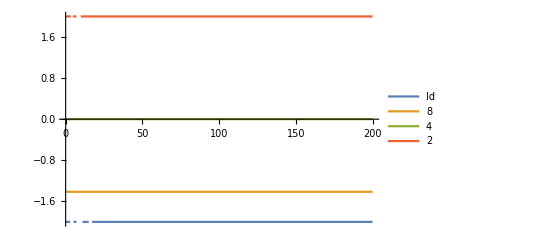

```mathematica
T=1
B=100
Plot[{Xij[{PauliMatrix[4],PauliMatrix[4]}, 1, 2]//FullSimplify,Xij[{P8,PauliMatrix[4]}, 1, 2]//FullSimplify, Xij[{P4,PauliMatrix[4]}, 1, 2]//FullSimplify, Xij[{P2,PauliMatrix[4]}, 1, 2]//FullSimplify}, {ω, 0, 200},  PlotLegends->{"Id", "8",  "4","2"}, PlotRange->{-2,2}]
```

1000

0.1

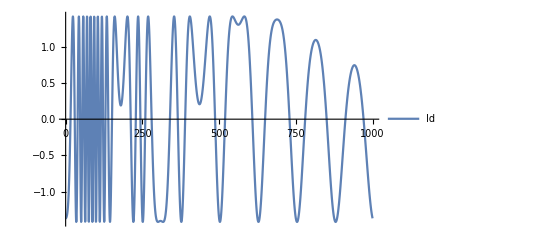

```mathematica
B=1000
T=.1
Plot[Xij[{P4,mP4, mP4, mP4}, 1, 2]//FullSimplify, {ω, 0, 1000},  PlotLegends->{"Id", "8",  "4","2"}, PlotRange->All]
```

```mathematica
NIntegrate[Theta[T, T/2] * Theta[T/2, 0] *Xij[{mP4, mP4}, 1, 2], {ω, 0, 10000}]

(*NIntegrate[Theta[T, T/2] * Theta[T/2, 0] *Xij[{PauliMatrix[4],PauliMatrix[4]}, 1, 2], {ω, 0, 10000}]*)
```

NIntegrate::levmaxord: ((√2 Cos[Times[«2»]] Sin[Times[«2»]]+(Times[«2»]+Power[«2»])/(√2)) ((Times[«3»]+Times[«3»]) (Times[«2»]+Times[«3»])+(Times[«3»]+Times[«3»]) («1»))+(«1») («1»))/(√2)+((√2 Cos[Times[«2»]] Sin[Times[«2»]]+«1») «1»«1»«1»)/(√2)+(«1»)/(√2)+((√2 Cos[Times[«2»]] Sin[Times[«2»]]+(Power[«2»]+«1»)/(√2)) («1»)+(«1») («1»))/(√2) is a Levin function of differential order 64 which exceeds value of option "MaxOrder" -> 50. Treating ((√2 Cos[Times[«2»]] Sin[Times[«2»]]+(Times[«2»]+Power[«2»])/(√2)) ((Times[«3»]+Times[«3»]) (Times[«2»]+Times[«3»])+(Times[«3»]+Times[«3»]) («1»))+(«1») («1»))/(√2)+((√2 Cos[Times[«2»]] Sin[Times[«2»]]+«1») «1»«1»«1»)/(√2)+(«1»)/(√2)+((√2 Cos[Times[«2»]] Sin[Times[«2»]]+(Power[«2»]+«1»)/(√2)) («1»)+(«1») («1»))/(√2) as a non-Levin function.

{{0.00553034}}

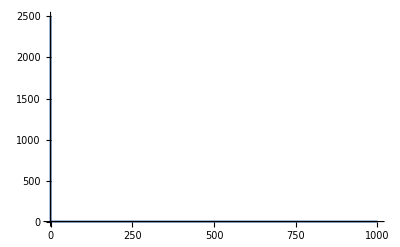

```mathematica
Plot[Theta[T, T/2] * Theta[T/2, 0], {ω, 0, 1000}, PlotRange->All]
```

```mathematica
Integrate[Theta[T/4, 0] * Theta[T, 3*T/4] *MatrixExp[-ⅈ * (Theta[T/4, 0] + Theta[T, 3*T/4] - Theta[3*T/4, T/2]  )PauliMatrix[4]][[1]][[1]], {ω, 0, ∞}]
```

∫_0^∞ (ⅇ^(-(ⅈ (Sin[0.025 ω]+Sin[0.05 ω]-2 Sin[0.075 ω]+Sin[0.1 ω]))/ω) Sin[0.025 ω] (-Sin[0.075 ω]/ω+Sin[0.1 ω]/ω))/ω ⅆω

```mathematica
Series[MatrixExp[-ⅈ * (Theta[t + δ, t])*PauliMatrix[4]][[1]][[1]], {δ, 0, 5}]
```

1-ⅈ Cos[t ω] δ+1/2 (-Cos[t ω]^2+ⅈ ω Sin[t ω]) δ^2+1/6 ⅈ (ω^2 Cos[t ω]+Cos[t ω]^3-3 ⅈ ω Cos[t ω] Sin[t ω]) δ^3+1/24 (4 ω^2 Cos[t ω]^2+Cos[t ω]^4-ⅈ ω^3 Sin[t ω]-6 ⅈ ω Cos[t ω]^2 Sin[t ω]-3 ω^2 Sin[t ω]^2) δ^4-1/120 ⅈ (ω^4 Cos[t ω]+10 ω^2 Cos[t ω]^3+Cos[t ω]^5-15 ⅈ ω^3 Cos[t ω] Sin[t ω]-10 ⅈ ω Cos[t ω]^3 Sin[t ω]-15 ω^2 Cos[t ω] Sin[t ω]^2) δ^5+O[δ]^6

```mathematica
Series[Exp[-ω], {ω, 0, 5}]
```

1-ω+ω^2/2-ω^3/6+ω^4/24-ω^5/120+O[ω]^6

```mathematica
Integrate[Theta[t4, t3] * Theta[t2 , t1] * Cos[ω*t5]  , {ω, 0 ,∞}]
```

ConditionalExpression[(π (4 (t1-t2) t4 Abs[t3]-4 t1 t3 Abs[t4]+t3 t4 (Abs[t2+t4-t5]-Abs[t2-t4+t5]-Abs[-t2+t4+t5]+Abs[t2+t4+t5])))/(8 t3 t4), ]

```mathematica
Integrate[Theta[t4, t3] * Theta[t2 , t1] * Cos[ω*t5]* Cos[ω*t6]  , {ω, 0 ,∞}]
```

ConditionalExpression[-1/16 π (4 Abs[t1-t3]-4 Abs[t2-t3]-4 Abs[t1+t3]+4 Abs[t2+t3]-4 Abs[t1-t4]+4 Abs[t1+t4]-Abs[t2+t4-t5-t6]+Abs[t2-t4+t5-t6]-Abs[t2+t4+t5-t6]+Abs[t2-t4-t5+t6]-Abs[t2+t4-t5+t6]+Abs[t2-t4+t5+t6]+Abs[-t2+t4+t5+t6]-Abs[t2+t4+t5+t6]), ]

```mathematica
Integrate[Theta[t4, t3] * Theta[t2 , t1] * Cos[ω*t5]* Cos[ω*t6]* Cos[ω*t7]  , {ω, 0 ,∞}]
```

∫_0^∞ Cos[t5 ω] Cos[t6 ω] Cos[t7 ω] (-Sin[t1 ω]/ω+Sin[t2 ω]/ω) (-Sin[t3 ω]/ω+Sin[t4 ω]/ω)ⅆω